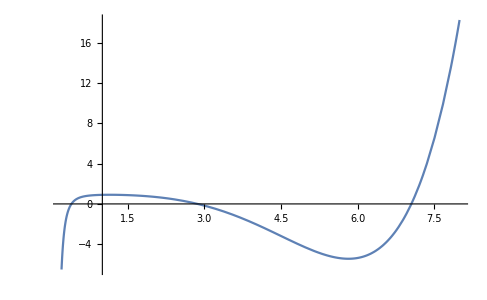

```mathematica
Clear[k,m,ss,om,jj];
(*m1r=k r^3;
m2r=m;
msr= 4 Pi ss r^2;*)
k=0.01;
m=1;
om=0.2;  (* ω *)
jj=0.1;
Omega=2 jj/x^3;  (* Ω *)
ss=0.01;
p0=1/2(x Omega D[Omega,{x,1}]- om Omega);
p2=(x om^2)/(x-2)-(om^2+Omega^2)/(1-2k m^2 x^2)+(x m Omega D[Omega,{x,1}])/(2-4k m^2 x^2);
p4=(x^2 om^2)/(x-2)^2-(Omega^2-om Omega+om^2)/((1-2k m^2 x^2)^2);
q0=m^4 x^3(1-k m^2 x^3-8 π^2 ss^2 m^2 x^3)p0-4 m^4 x^3(4 π^2 ss^2 x+k)+m^2(8 π^2 ss^2 m^2 x^3+1+k m^2 x^3)^2;
q2=m^4 x^3(-16 π^2 ss^2 x+(16 π^2 ss^2 x^5 m^3 om^2)/(x-2)+(1-k m^2 x^3-8 π^2 ss^2 x^3 m^2)p2);
q4=m^4 x^3((1-k m^2 x^3-8 π^2 ss^2 m^2 x^3)p4 +(16 π^2 ss^2 x^5 m^2 om^2)/(x-2)^2);
f1=Plot[q0,{x,0.2, 8},PlotRange->All]
```

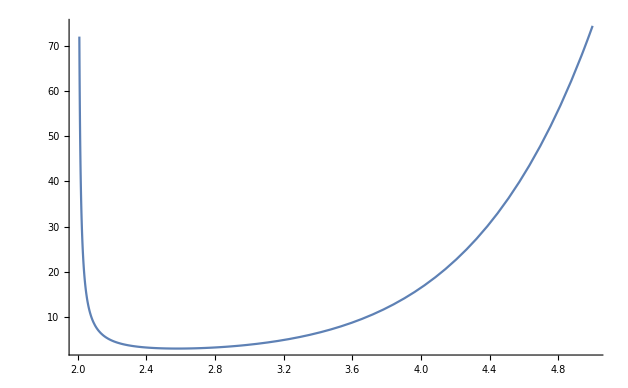

```mathematica
f1a=Plot[q2,{x,2.01, 5},PlotRange->All]
```

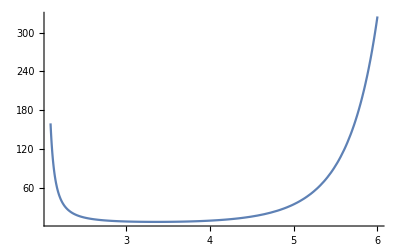

```mathematica
f1b=Plot[q4,{x,2.1, 6},PlotRange->All]
```

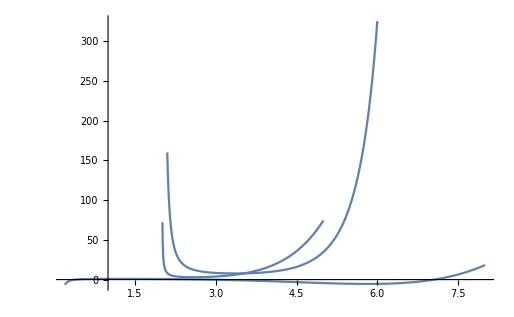

```mathematica
Show[f1,f1a,f1b]
```

```mathematica
q01=FullSimplify[q0]
```

0.981074-0.06/x^3-0.00385072 x^3-0.0157914 x^4+0.000320255 x^6

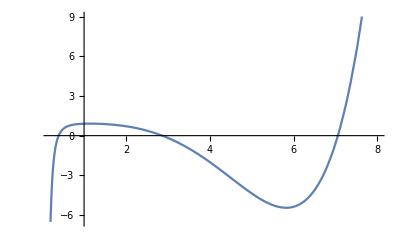

```mathematica
Plot[q01,{x,0.2,8}]
```

```mathematica
q01p=D[q01,x]
```

0.18/x^4-0.0115522 x^2-0.0631655 x^3+0.00192153 x^5

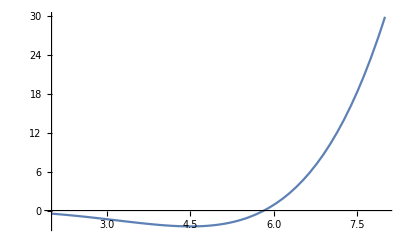

```mathematica
Plot[q01p,{x,2,8},PlotRange->All]
```

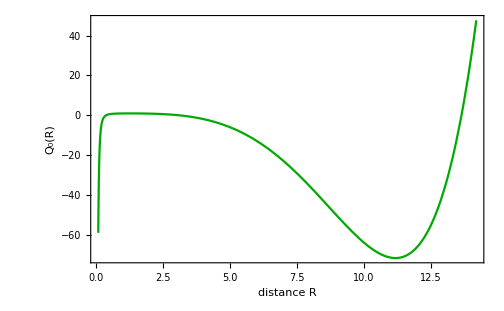

```mathematica
Clear[k,m,ss,om,jj];(*m1r=k r^3; m2r=m; msr= 4 Pi ss r^2;*)
k=0.001;
m=1;
om=0.2;  (* ω *)
jj=0.1;
Omega=2 jj/x^3;  (* Ω *)
ss=0.01;
p0=1/2(x Omega D[Omega,{x,1}]- om Omega);
p2=(x om^2)/(x-2)-(om^2+Omega^2)/(1-2k m^2 x^2)+(x m Omega D[Omega,{x,1}])/(2-4k m^2 x^2);
p4=(x^2 om^2)/(x-2)^2-(Omega^2-om Omega+om^2)/((1-2k m^2 x^2)^2);
q0a=m^4 x^3(1-k m^2 x^3-8 π^2 ss^2 m^2 x^3)p0-4 m^4 x^3(4 π^2 ss^2 x+k)+m^2(8 π^2 ss^2 m^2 x^3+1+k m^2 x^3)^2;
q2a=m^4 x^3(-16 π^2 ss^2 x+(16 π^2 ss^2 x^5 m^3 om^2)/(x-2)+(1-k m^2 x^3-8 π^2 ss^2 x^3 m^2)p2);
q4a=m^4 x^3((1-k m^2 x^3-8 π^2 ss^2 m^2 x^3)p4 +(16 π^2 ss^2 x^5 m^2 om^2)/(x-2)^2);
f2=Plot[q0a,{x,0.1,14.2},Frame->True,FrameLabel->{"distance R"," Q_0(R)"},PlotStyle->{Darker[Green]},AxesStyle->Black,LabelStyle->{FontFamily->"Arial",11,GrayLevel[0],Bold}]
```

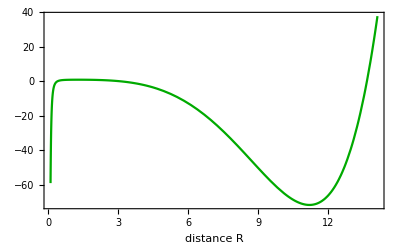

```mathematica
f20=Plot[q0a,{x,0.1,14.1},Frame->True,FrameLabel->{"distance R",""},PlotStyle->{Darker[Green]},AxesStyle->Black,LabelStyle->{FontFamily->"Arial",11,GrayLevel[0],Bold}]
```

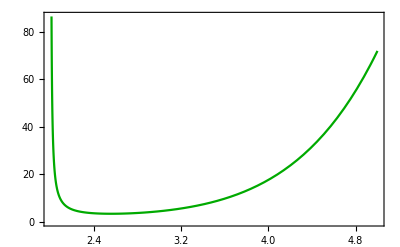

```mathematica
f2a=Plot[q2a,{x,2,5},Frame->True,PlotStyle->{Darker[Green]},AxesStyle->Black,LabelStyle->{FontFamily->"Arial",11,GrayLevel[0],Bold}]
```

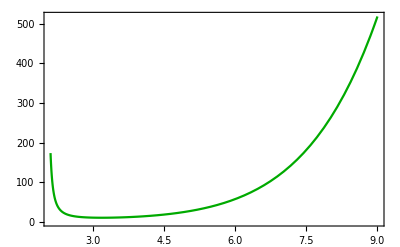

```mathematica
f2b=Plot[q4a,{x,2.1,9},Frame->True,PlotStyle->{Darker[Green]},AxesStyle->Black,LabelStyle->{FontFamily->"Arial",11,GrayLevel[0],Bold}]
```

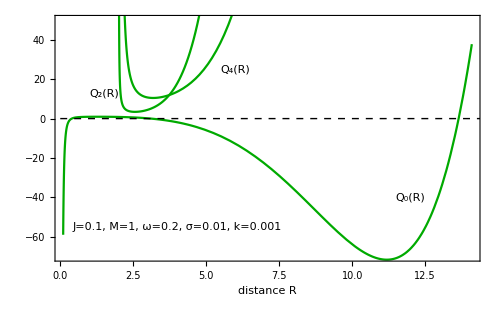

```mathematica
fig2a=Show[f20,f2a,f2b, Graphics[{Inset[Framed["J=0.1, M=1, ω=0.2, σ=0.01, k=0.001"],{4,-55},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",12}]}],Graphics[{Inset["Q_2(R)",{1.5,13},BaseStyle->{Italic,Bold,Purple,FontFamily->"Times",12}]}],Graphics[{Inset["Q_0(R)",{12,-40},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",12}]}],Graphics[{Inset["Q_4(R)",{6,25},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",12}]}],FrameStyle->Directive[Black,Thick],Epilog->{{Dashed,Black,Line[{{0,0},{20,0}}]}},BaseStyle->{Large,Italic,Bold,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],ImageSize->500,PlotRange->{-70,50}]
```

```mathematica
Export["D:fig2a.pdf",fig2a,"PDF"];
Export["D:fig2a.eps", fig2a];
```

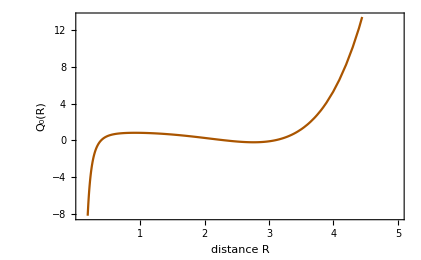

```mathematica
Clear[k,m,ss,om,jj];(*m1r=k r^3; m2r=m; mmsr= 4 Pi ss r^2;*)
k=0.05;
m=1;
om=0.2;  (* ω *)
jj=0.1;
Omega=2 jj/x^3;  (* Ω *)
ss=0.01;
p0=1/2(x Omega D[Omega,{x,1}]- om Omega);
p2=(x om^2)/(x-2)-(om^2+Omega^2)/(1-2k m^2 x^2)+(x m Omega D[Omega,{x,1}])/(2-4k m^2 x^2);
p4=(x^2 om^2)/(x-2)^2-(Omega^2-om Omega+om^2)/((1-2k m^2 x^2)^2);
q0b=m^4 x^3(1-k m^2 x^3-8 π^2 ss^2 m^2 x^3)p0-4 m^4 x^3(4 π^2 ss^2 x+k)+m^2(8 π^2 ss^2 m^2 x^3+1+k m^2 x^3)^2;
q2b=m^4 x^3(-16 π^2 ss^2 x+(16 π^2 ss^2 x^5 m^3 om^2)/(x-2)+(1-k m^2 x^3-8 π^2 ss^2 x^3 m^2)p2);
q4b=m^4 x^3((1-k m^2 x^3-8 π^2 ss^2 m^2 x^3)p4 +(16 π^2 ss^2 x^5 m^2 om^2)/(x-2)^2);
f3=Plot[q0b,{x,0.1,5},Frame->True,FrameLabel->{"distance R","Q_0(R)"},PlotStyle->{Darker[Orange]},AxesStyle->Black,LabelStyle->{FontFamily->"Arial",11,GrayLevel[0],Bold}]
```

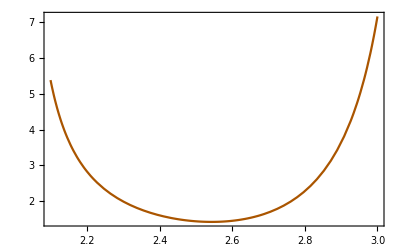

```mathematica
f3a=Plot[q2b,{x,2.1,3},Frame->True,PlotStyle->{Darker[Orange]},AxesStyle->Black,LabelStyle->{FontFamily->"Arial",11,GrayLevel[0],Bold}]
```

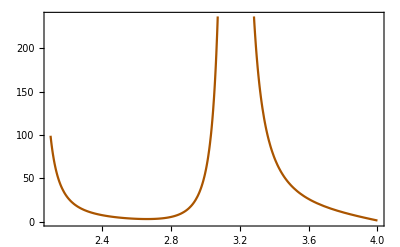

```mathematica
f3b=Plot[q4b,{x,2.1,4},Frame->True,PlotStyle->{Darker[Orange]},AxesStyle->Black,LabelStyle->{FontFamily->"Arial",11,GrayLevel[0],Bold}]
```

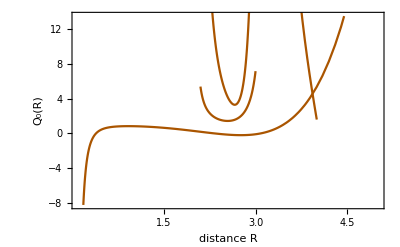

```mathematica
Show[f3,f3a,f3b]
```

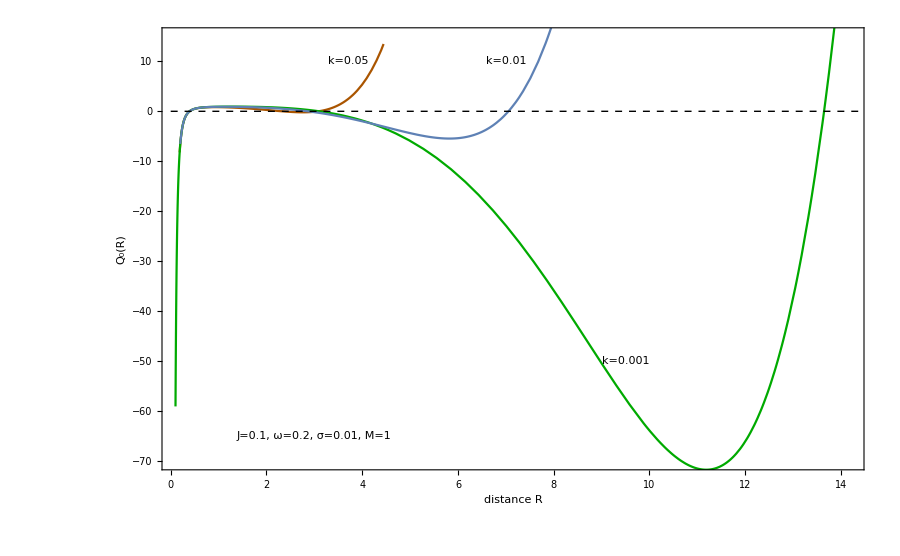

```mathematica
fd02=Show[f3,f2,f1,Graphics[{Inset[Framed["J=0.1, ω=0.2, σ=0.01, M=1"],{3,-65},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",12}]}],Graphics[{Inset["k=0.05",{3.7,10},BaseStyle->{Italic,Bold,Purple,FontFamily->"Times",12}]}],Graphics[{Inset["k=0.001",{9.5,-50},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",12}]}],Graphics[{Inset["k=0.01",{7,10},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",12}]}],FrameStyle->Directive[Black,Thick],Epilog->{{Dashed,Black,Line[{{0,0},{20,0}}]}},BaseStyle->{Large,Italic,Bold,FontFamily->"Times",18},ImageSize->900,PlotRange->{-70,15},Axes->False]
```

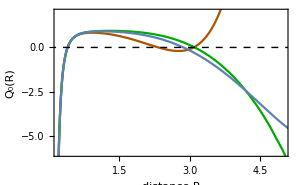

```mathematica
fd02small=Show[f3,f2,f1,Graphics[{Inset[Framed["J=0.1, ω=0.2, σ=0.01, M=1"],{50,-5},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",12}]}],FrameStyle->Directive[Black,Thick],Epilog->{{Dashed,Black,Line[{{0,0},{20,0}}]}},BaseStyle->{Large,Italic,Bold,FontFamily->"Times",18},ImageSize->300,PlotRange->{{0.2,5},{-6,2}},Axes->False]
```

```mathematica
Export["D:fd02.pdf",fd02,"PDF"];
Export["D:fd02.eps", fd02];
```

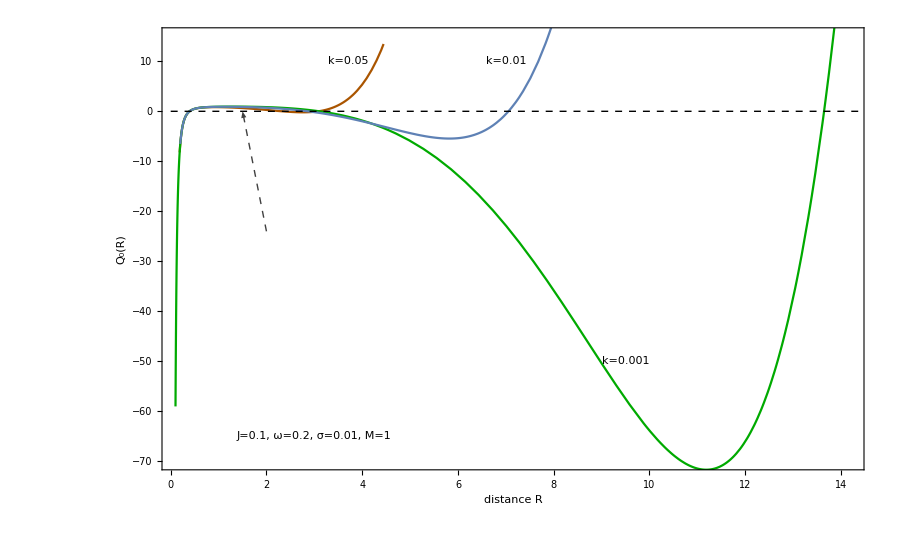

```mathematica
fig2=Show[fd02,Epilog->{Inset[fd02small,Scaled[{0.25,0.35}]],Dashed,Darker[Gray,0.5],Arrowheads[Medium],Arrow[{{2,-24},{1.5,0}}],BaseStyle->{Italic,Bold,Black,FontFamily->"Times",12},{Dashed,Black,Line[{{0,0},{20,0}}]}},LabelStyle->Directive[Black,Large]]
```

```mathematica
Export["D:fig2.pdf",fig2,"PDF"];
Export["D:fig2.eps", fig2];
```